```mathematica
Clear[condition]
```

```mathematica
condition[x_]:=(#[[1]]+#[[2]]≤1 && #[[1]]#[[2]]<=x)&
```

```mathematica
condition[2/9][{0.6,0.5}]
```

False

```mathematica
Solve[{x+y==1,x y ==w},{x,y}]
```

{{x→1/2 (1-√(1-4 w)),y→1/2 (√(1-4 w)+1)},{x→1/2 (√(1-4 w)+1),y→1/2 (1-√(1-4 w))}}

```mathematica
Solve[1-4w==4/81,w]
```

{{w→77/324}}

```mathematica
Options[RegionPlot]
```

{AlignmentPoint→Center,AspectRatio→1,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&,#2&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→Full,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,TargetUnits→Automatic,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ken_l/Documents/ps/images

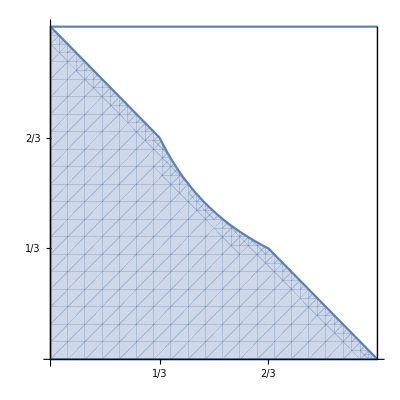

```mathematica
RegionPlot[condition[2/9][{x,y}],{x,0,1},{y,0,1},Frame->False]//Show[{Plot[1,{x,0,1},PlotRange->{{0,1},{0,1}}],#},Ticks->{{1/3,2/3},{1/3,2/3}},AspectRatio->1,Epilog->{Line[{{1,0},{1,1}}]}]&
```

```mathematica
RegionPlot[condition[2/9][{x,y}],{x,0,1},{y,0,1},Frame->False]//Show[{Plot[1,{x,0,1},PlotRange->{{0,1},{0,1}}],#},Ticks->{{1/3,2/3},{1/3,2/3}},AspectRatio->1,Epilog->{Line[{{1,0},{1,1}}]}]&//Export["fig-geom-prob.png",#,"PNG"]&
```

```mathematica
Integrate[(1-x)-3/(16x),{x,1/4,3/4}]
```

1/16 (4-3 log(3))

```mathematica
N[%]
```

0.0440102

```mathematica
Manipulate[{RegionPlot[condition[w][{x,y}],{x,0,1},{y,0,1}],Solve[{x+y==1,x y ==w,x>0,y>0},{x,y}]},{w,1/20,1/2,1/20}]
```

```mathematica
3/16
```

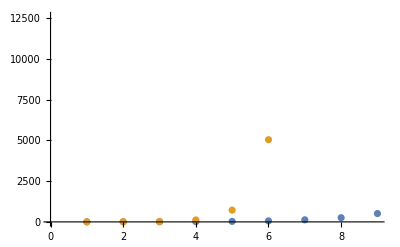

```mathematica
ListPlot[{Map[2^(#-1)&,Range[2,10]],Map[#!&,Range[2,10]]}]
```